# Occultation Forward Modeling Notebook Hosea Siu

## Constant Declarations

```mathematica
{TOL,NAvagadro,R,k,G,αN2,MN2,MPluto,rPluto,distToObserver, impactParameter}=ToExpression[Import["/Users/Hosea/Dropbox (MIT)//Academic/12.ThG/AtmosphereCode/constants.xlsx",{"Data",1}][[;;,2]]];
```

## General Helper Functions

```mathematica
(* local gravity as a function of r and M*)
gravity[r_, MPlanet_] := G*MPlanet/r^2;

(* barometric formula - pressure as a function of height for isothermal atmospheres only *)
barometric[p0_, M_, h_, T_, r0_, MPlanet_] := p0 E^((-M gravity[h + r0, MPlanet] h)/(R T));

(* get the slope and y-intercept from 2 points - used for resolving linearly-varying values between atmosphere boundaries *)
slopeInterceptFrom2Pts[x1_,y1_,x2_,y2_]:=Module[{m,b},m=(y1-y2)/(x1-x2);
b=y1-m x1;
Return[{m,b}];];
```

## Atmosphere Generation

### Physical Equations

```mathematica
(*Lorentz-Lorenz Equation for n values close to 1:returns a refractive index n given a temperature and pressure*)
(*lorentzLorenz[α_,p_,T_]:=SetPrecision[√(1+(4 π NAvagadro α p)/(R T)),100];*)

(* exact version of LL equation *)
lorentzLorenzExact[α_,p_,T_]:=Module[{n,sols},
sols = NSolve[(n^2-1)/(n^2+2)== (4 π NAvagadro p α)/(3 R T),n];
Return[First[Select[n/.sols,#≥ 0&]]];
];
```

### Helper Functions

```mathematica
setAtmProperty[startValue_,stopValue_,numShells_]:=Module[{},
If[
startValue==stopValue, (* no variation *)
ConstantArray[startValue,numShells],

(* linear variation *)
Range[startValue,stopValue,N[(stopValue-startValue)/(numShells-1)]]
]
];

makeAtmosphereSection[r0_,r1_,MPlanet_,sectionShells_,T0_,T1_,M0_,M1_,P0_,αz0_,αz1_,α0_,α1_]:=Module[{radii,temps,M,pressures,ρn,dP,mM,bM,mT,bT,P,r,i,αz,α,𝒩},
{mM,bM}=slopeInterceptFrom2Pts[r0,M0,r1,M1];
{mT,bT}=slopeInterceptFrom2Pts[r0,T0,r1,T1];
radii=setAtmProperty[r0,r1,Round[sectionShells]]; (* rounding in case sectionShells is not passed in as an integer *)
M=setAtmProperty[M0,M1,Round[sectionShells]]; (* meam molecular mass, not planet mass *)
temps=setAtmProperty[T0,T1,Round[sectionShells]];
αz=setAtmProperty[αz0,αz1,Round[sectionShells]]; (* attenuation coefficient *)
α=setAtmProperty[α0,α1,Round[sectionShells]]; (* mean polarizability *)
pressures={P0};ρn={P0/(k temps⟦1⟧)};
dP={ρn⟦1⟧ M⟦1⟧};
𝒩={lorentzLorenzExact[α[[1]],pressures[[1]],temps[[1]]]-1};

Do[AppendTo[pressures,Re[DSolveValue[{P'[r]==-((mM r+bM) P[r] (G MPlanet))/((mT r+bT) R r^2),P[r0]==P0},P[radii⟦i⟧],r]]];AppendTo[ρn,pressures⟦i⟧/(k temps⟦i⟧)];AppendTo[dP,ρn⟦i⟧ M⟦i⟧];
AppendTo[𝒩,lorentzLorenzExact[α[[i]],pressures[[i]],temps[[i]]]-1];,
{i,2,Length[radii]}
];
Return[{radii,temps,M,pressures,ρn,αz,α,𝒩}];
];

joinAtmosphereSections[sections_]:=Module[{radii,temps,M,pressures,ρn,αz,α,𝒩,currentSection},
radii={};
temps={};
M={};
pressures={};
ρn={};
αz={};
α={};
𝒩={};

Do[
currentSection=sections[[i]];
If[i≠ 1,
Do[
(* if the current section that we're looking at isn't the bottome section, drop the bottommost shell, because it's a duplicate of the one below it *)
currentSection[[i]]=Drop[currentSection[[i]],1];,
{i,1,Length[currentSection]}
];
];
radii=Join[radii,currentSection⟦1⟧];temps=Join[temps,currentSection⟦2⟧];M=Join[M,currentSection⟦3⟧];pressures=Join[pressures,currentSection⟦4⟧];ρn=Join[ρn,currentSection⟦5⟧];
αz=Join[αz,currentSection[[6]]];
α=Join[α,currentSection[[7]]];
𝒩=Join[𝒩,currentSection[[8]]];,
{i,1,Length[sections]}
];
Return[{radii,temps,M,pressures,ρn,αz,α,𝒩}];
];
```

### Atomsphere Generation Functions

```mathematica
makeAtmosphere[boundaryR_,boundaryT_,boundaryM_,sectionShells_,P0_,boundaryαz_,boundaryα_,MPlanet_,exportFolderPath_: Null,atmosphereNumber_: Null]:=Module[{numSections,atmSections,section,PRef,atmosphere,header,fullPath},numSections=Length[sectionShells];
atmSections={};
PRef=P0;
If[Length[boundaryR]≠numSections+1||Length[boundaryT]≠numSections+1||Length[boundaryM]≠numSections+1,
Print["invalid number of arguments in MakeAtmosphere"];
Return[];
];
Do[
section=makeAtmosphereSection[boundaryR[[i]],boundaryR[[i+1]],MPlanet,sectionShells[[i]],boundaryT[[i]],boundaryT[[i+1]],boundaryM[[i]],boundaryM[[i+1]],PRef,boundaryαz[[i]],boundaryαz[[i+1]],boundaryα[[i]],boundaryα[[i+1]]];
PRef=Last[section[[4]]];
AppendTo[atmSections,section];,
{i,1,numSections}
];
atmosphere=joinAtmosphereSections[atmSections];
header={{boundaryR,boundaryT,boundaryM,sectionShells,P0,boundaryαz,boundaryα,MPlanet}};
If[StringQ[exportFolderPath],If[IntegerQ[atmosphereNumber],fullPath=exportFolderPath<>"/constructedAtmosphere"<>IntegerString[atmosphereNumber]<>".tsv";,fullPath=exportFolderPath<>"/constructedAtmosphere"<>".tsv";];
Export[fullPath,Join[header,atmosphereᵀ],"Table"];
(*Print["exported atmosphere to "<>fullPath];*)
];
Return[atmosphere];
];

(*same as version above,but allows all parameters to be passed in via a single list (of lists and numbers)*)(*allows for easier editing of parameters when making a range of atmospheres*)makeAtmosphere[params_,exportFolderPath_: Null,atmosphereNumber_: Null]:=Module[{},Return[makeAtmosphere[params[[1]],params[[2]],params[[3]],params[[4]],params[[5]],params[[6]],params[[7]],params[[8]],exportFolderPath,atmosphereNumber];];];

(* make a set of atmospheres based on one variable property *)
makeAtmosphereSet[baseAtm_,exportFolderPath_,variableProperty_,initNum_: 1]:=Module[{atmNum,varRange,currentAtm,arrayPosition,propertyNum,prop,error},
error=False;
(*check for specification problems*)
If[Length[variableProperty]≠5||!StringQ[variableProperty[[1]]],
Print["variableProperty specification length or property error"];
error=True;
];
If[error,Return[]];
Do[
(*make sure all specs are positive*)
If[variableProperty[[i]]≤0,
Print["zero or negative value in variableProperty specification"];
error=True;
],
{i,1,Length[variableProperty]}];
If[error,Return[]];
atmNum=initNum;
varRange=Range[variableProperty[[3]],variableProperty[[4]],variableProperty[[5]]];
arrayPosition=variableProperty[[2]];
prop=ToLowerCase[variableProperty[[1]]];
Which[(*figure out which property we want to change*)
prop=="r",propertyNum=1,
prop=="t",propertyNum=2,
prop=="m",propertyNum=3,
prop=="s"||prop=="shells"||prop=="sectionshells",propertyNum=4,
prop=="p0",propertyNum=5,
prop=="αz",propertyNum=6,
prop== "α", propertyNum = 7,
prop=="mplanet",propertyNum=8,
True,Print["property request error"];Return[];
];
(*check constraints on radius*)
If[propertyNum==1,(*if the variable we're trying the change is the radius*)Do[Which[arrayPosition≠1&&arrayPosition≠Length[baseAtm[[propertyNum]]],(*if it's not the first or the last radius boundary*)If[varRange[[i]]<baseAtm[[propertyNum,i-1]]||varRange[[i]]>baseAtm[[propertyNum,i+1]],
Print["radius range specification error"];
error=True;
];,
arrayPosition==1,
(*bottommost boundary*)
If[varRange[[i]]>baseAtm[[propertyNum,i+1]],
Print["radius range specification error"];
error=True;];,
arrayPosition==Length[baseAtm[[propertyNum]]],
(*topmost boundary*)
If[varRange[[i]]<baseAtm[[propertyNum,i-1]],
Print["radius range specification error"];
error=True;
];,
True,(*boundary spec error*)
Print["radius boundary specification error"];
error=True;
];,
{i,1,Length[varRange]}];
];
If[error,Return[]];
(*make the atmospheres*)
Do[currentAtm=baseAtm;
currentAtm[[propertyNum,arrayPosition]]=varRange[[i]];
makeAtmosphere[currentAtm,exportFolderPath,atmNum];
atmNum=atmNum+1;,{i,1,Length[varRange]}];
];
```

### Graphics Functions

```mathematica
plotAtmosphereProperties[atmosphere_]:=Module[{TPlot,PPlot,MPlot,ρnPlot,αzPlot,αPlot,𝒩Plot,atm},
If[StringQ[atmosphere],
atm=Import[atmosphere,"HeaderLines"-> 1]ᵀ;,
atm=atmosphere;
];

TPlot=ListPlot[ArrayReshape[Riffle[atm⟦2⟧,atm⟦1⟧],{Length[atm⟦1⟧],2}],PlotLabel->"temperature (K)",Filling-> Axis,PlotRange->{Min[atm[[1]]],All}];
MPlot=ListPlot[ArrayReshape[Riffle[atm⟦3⟧,atm⟦1⟧],{Length[atm⟦1⟧],2}],PlotLabel->"M (kg/mol)",Filling->Axis,PlotRange->{Min[atm[[1]]],All}];
PPlot=ListPlot[ArrayReshape[Riffle[atm⟦4⟧,atm⟦1⟧],{Length[atm⟦1⟧],2}],PlotLabel->"pressure (Pa)",Filling->Axis,PlotRange->{Min[atm[[1]]],All}];ρnPlot=ListPlot[ArrayReshape[Riffle[atm⟦5⟧,atm⟦1⟧],{Length[atm⟦1⟧],2}],PlotLabel->"number density",Filling->Axis,PlotRange->{Min[atm[[1]]],All}];
αzPlot=ListPlot[ArrayReshape[Riffle[atm[[6]],atm[[1]]],{Length[atm[[1]]],2}],PlotLabel->"α_z",Filling->Axis,PlotRange->{Min[atm[[1]]],All}];
αPlot=ListPlot[ArrayReshape[Riffle[atm[[7]],atm[[1]]],{Length[atm[[1]]],2}],PlotLabel->"α",Filling->Axis,PlotRange->{Min[atm[[1]]],All}];

(* this one's a little different *)
𝒩Plot=ListPlot[ArrayReshape[Riffle[atm[[8]],atm[[1]]],{Length[atm[[1]]],2}],PlotLabel->"refractivity (𝒩)",Filling->Axis,PlotRange->{Min[atm[[1]]],All}];
Return[{TPlot,MPlot,PPlot,ρnPlot,αzPlot,αPlot,𝒩Plot}];
];
```

## Lightcurve Generation

### Physical Equations

```mathematica
(*refraction as a function of angles and rafractivity indicies*)
snellsLaw[θIn_,nIn_,nOut_]:=If[nIn==nOut,θIn,ArcSin[Sin[θIn] nIn/nOut]];

(*decrease the flux of a single light beam based on the linear approximation of the Beer-Lambert law*)
beerLambert[αz_,flux_,z_]:=flux E^(-αz z);
```

### Helper Functions

```mathematica
(*shells are composed of the following:the circle graphic,the circle equation,the circle radius,the n value,and the attenuation coefficient αz*)
(*note that attenuation coefficient is represented here as αz rather than α because the letter also stands for mean polarizability,which is used elsewhere in this program;αz implies it's a function of z-the distance the beam of light travelled in the material*)
shell[r_,n_,αz_]:=Module[{x,y},Return[{Circle[{0,0},r],x^2+y^2==r^2,r,n,αz}];]

(*calculate the normal angle of a shell based on location,assuming shells centered at 0,0)*)
normalAngle[point_]:=ArcTan[point[[1]],point[[2]]];

(*helper function to negate the y term of an xy pair for flipping atmospheric intersection points*)
flipY[x_,y_]:=Return[{x,-y}];

(*find the next location of an intersection given a ray *)
findNextShellIntersection[radius_,rayPosition_,rayAngle_]:=Module[{x0,y0,m,t1,t2,tList},(*TODO-can't I just figure out radius from position?*)x0=rayPosition[[1]];
y0=rayPosition[[2]];
m=Tan[rayAngle];
t1=(-x0-m y0+√(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
t2=(-x0-m y0-√(radius^2 (1+m^2)-(y0-m x0)^2))/(1+m^2);
tList=Select[{t1,t2},(#∈Reals&&#>TOL)&] (*return only real positive time values*)
];

(* function that identifies where the light currently is in relation to shells *)
locateLightRay[position_,atm_]:=Module[{shellRadii,posRadius,difference,shellNum,rayLocation},
shellRadii = atm[[All,3]];
posRadius = Norm[position];
Which[
(* entirely outside of shells *)
posRadius > Last[shellRadii],
rayLocation = "outside",

(* entirely inside the inner shell *)
posRadius < First[shellRadii],
rayLocation = "inside",

(* on outer shell *)
Abs[Last[shellRadii]- posRadius]<TOL,
rayLocation = "on outer shell",

True,
{
Do[
difference = Abs[posRadius-shellRadii[[i]]];
If[difference<TOL,
shellNum = i;
rayLocation="on";
Break[];,
rayLocation = "between";
];,
{i,Length[atm]}
]
}
];
Return[rayLocation];
];

(* get the breakpoints in the interpolating functions for lightcurve generation *)
(* the magnitude and density interpolations have slightly different domains,so we have to choose the intersections of their domains *)
getBreakpoints[magFunc1_,densityFunc1_,magFunc2_,densityFunc2_]:=Module[{x1,x2,x3,x4},
x1=Max[magFunc1[[1,1,1]],densityFunc1[[1,1,1]]];(*max of right side minimum*)
x2=Min[magFunc1[[1,1,2]],densityFunc1[[1,1,2]]];(*min of right side maximum*)
x3=Max[magFunc2[[1,1,1]],densityFunc2[[1,1,1]]];(*max of left side minimum*)
x4=Min[magFunc2[[1,1,2]],densityFunc2[[1,1,2]]];(*min of left side maximum*)
Return[{x1,x2,x3,x4}];
]

(* import a constructed atmosphere and make a "shells" model of it *)
makeAtmosphereFromOpticalParams[params_, rArrayPos_: 1, 𝒩ArrayPos_: 8, αzArrayPos_: 6] := Module[{i, r, 𝒩, αz,paramAtmosphere,n,msg,layersPrint,layers},
layers = Length[params];
   paramAtmosphere = {};
msg = PrintTemporary["Generating atmosphere model with impact parameter of " <> ToString[impactParameter]];
layersPrint = PrintTemporary["layers " <> ToString[layers]];
   Do[
If[impactParameter== 0,
r=ToExpression[params[[i,rArrayPos]]];,
(* modify the effective radii of the atmosphere shells based on the impact parameter of the transit *)
r=√(ToExpression[params[[i,rArrayPos]]]^2-impactParameter^2);
];
Which[i==1,
atmMin=r;,

i== layers,
atmMax=r;
];
n = SetPrecision[ToExpression[params[[i, 𝒩ArrayPos]]] + 1, 64];
     αz = ToExpression[params[[i, αzArrayPos]]];
     paramAtmosphere = Append[paramAtmosphere, shell[r, n, αz]];, 
{i, 1, layers}];
atmStep = (atmMax-atmMin)/layers;
NotebookDelete[msg];
NotebookDelete[layersPrint];
   Return[paramAtmosphere];
];
```

### Ray Tracing Functions

```mathematica
(* updates the light position based on current position, direction, and shells *)
moveLightRay[rayPath_,rayAngle_,atm_]:=Module[{location,tList,intersect,t,n2,αz,position,posRadius,shellNum,noIntersect,atEnd,distTravelledInShell},
extincted = False;
position = Last[rayPath];
posRadius = Norm[position];

location  = locateLightRay[position,atm];
Which[
(* only need to check the outermost shell *)
location == "outside",
{
t = Min[findNextShellIntersection[Last[atm][[3]],position,rayAngle]];
},

(* only need to check the innermost shell *)
location == "inside",
{
t = Min[findNextShellIntersection[First[atm][[3]],position,rayAngle]];
},

(* only need to check the second-outermost and itself shell unless it's a one-shell atmosphere *)
location == "on outer shell",
{
If[Length[atm]>1,
(* if it's a multi-shell atmosphere *)
{
t = Min[Join[
findNextShellIntersection[atm[[-2,3]],position,rayAngle],
findNextShellIntersection[atm[[-1,3]],position,rayAngle]
]
];
},

(* else if it's a single-shell atmosphere *)
{
t = Min[findNextShellIntersection[atm[[1,3]],position,rayAngle]];
}
]
},

(* need to check the previous, current, and next shells *)
location == "on",
{
Do[
If[Abs[posRadius-atm[[All,3]][[i]]]<TOL,
shellNum = i;
Break[];,
];,
{i,Length[atm]}
];

If[shellNum==1,
(* if on inner shell - the innermost shell represents the planet itself *)
{
extincted = True;
t =0;
},

(* if on some other shell *)
t = Min[Join[
findNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle],
findNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
findNextShellIntersection[atm[[shellNum-1,3]],position,rayAngle]
]
]
];
},

(* need to check the shells that it is between- now use currentShell as a counter *)
location == "between",
{
Print["warning: between atmosphere layers - this shouldn't really happen"];
shellNum =Length[atm];
While[atm[[shellNum,3]] > posRadius,
shellNum-=1; 
];
tList = Join[
findNextShellIntersection[atm[[shellNum,3]],position,rayAngle],
findNextShellIntersection[atm[[shellNum+1,3]],position,rayAngle]
];
t= Min[tList];
}
];

(* stuff to be done regardless of ray location case *)
(* check for non-intersection case *)
noIntersect = False;
atEnd = False;
If[t==Infinity,
If[Length[rayPath]==1,
noIntersect = True;
];
atEnd = True;
t=distToObserver; (* move the end of the light beam to the observer position *)
];

intersect = {t+position[[1]],Tan[rayAngle] t + position[[2]]};
position = intersect;

(* figure out which we're now interacting with *)
Do[
If[Abs[Norm[position]-atm[[All,3]][[i]]]<TOL,
n2 = atm[[i,4]]; (* get the refractivity of the shell *)
If[!extincted && i>1,

αz=atm[[i-1,5]];, (* get the attenuation coefficient of the shell to the interior of this one *)

αz=0; (* if already extincted or in inner shell, this doesn't actually matter *)
];
Break[];,

(* if we're not interacting with a shell, then we're back in vacuum with n2 = 1.0 and αz = 0*)
n2 = 1.0;
αz=0;
];,
{i,Length[atm]}
];

(* if the light has not been entirely extincted yet, append the angle and final flux level to the appropriate lists *)
If[!extincted,
AppendTo[intersectionPoints,position];
Which[
noIntersect,
AppendTo[angleList,0.0];,

atEnd,
AppendTo[angleList,rayAngle];,

True,
AppendTo[angleList,refract[intersectionPoints,Last[angleList],n2]];

If[Length[intersectionPoints]>2 , (* if we're not at the starting point or first intersection point *)
distTravelledInShell = √((intersectionPoints[[Length[intersectionPoints],1]]-intersectionPoints[[Length[intersectionPoints]-1,1]])^2+(intersectionPoints[[Length[intersectionPoints],2]]-intersectionPoints[[Length[intersectionPoints]-1,2]])^2);,
distTravelledInShell=0;
];
currentRayFlux=beerLambert[αz,currentRayFlux,distTravelledInShell]; (* calculate light extinction *)
];
];
];

(*refract based on entry and shell conditions using Snell's Law*)refract[rayPath_,rayAngle_,n2_]:=Module[{newAngle,position,prevPosition,θ1,θ2,interactionType},position=Last[rayPath];
prevPosition=rayPath[[-2]];
interactionType=Null;
Which[(*hitting the same shell again*)
currentN==n2,
interactionType="same shell";

newAngle=rayAngle;,(*just grazed the top or bottom of a shell (no interaction),keep the angle the same*)
Abs[position[[1]]]<TOL,

interactionType="grazed";
newAngle=rayAngle;,

(*hitting shell from outside in (radius decreasing)*)
Norm[position]<Norm[prevPosition],
interactionType="outside in";
If[position[[2]]>0,
(*above the y=0 line*)
θ1=Mod[π-normalAngle[position]+rayAngle,π/2];
If[π/2-Abs[θ1]<10^-5,
Print[θ1];
Print[position];];
θ2=snellsLaw[θ1,currentN,n2];
newAngle=normalAngle[position]-π+θ2;,

(*on or below the y=0 line*)
θ1=Mod[normalAngle[position]-π-rayAngle,π/2];
θ2=snellsLaw[θ1,currentN,n2];
newAngle=normalAngle[position]-π-θ2;
];
,
(*hitting shell from inside out*)
Norm[position]>Norm[prevPosition]||Norm[position]==Norm[prevPosition],{interactionType="outside in";
If[position[[2]]>0,{
(*above the y=zero line*)
θ1=Mod[normalAngle[position]-rayAngle,π/2];
If[π/2-Abs[θ1]<10^-5,Print[θ1];
Print[position];];
θ2=snellsLaw[θ1,currentN,n2];
newAngle=normalAngle[position]-θ2;},{
(*on or below the y=0 line*)
θ1=Mod[rayAngle-normalAngle[position],π/2];
θ2=snellsLaw[θ1,currentN,n2];
newAngle=normalAngle[position]+θ2;}]}];
If[interactionType≠"grazed",currentN=n2;];
newAngle=Mod[newAngle,2 π];
(*TODO-probably more elegent way to do the angle formatting,because I basically want all angles to be near zero for readability*)
If[newAngle>3*π/4,
newAngle=newAngle-2*π;
];
Return[newAngle];
];

rayTrace[maxLightY_:1.5,minLightY_:0]:=Module[{extinctionY,beamsGenerated,beamsHittingAtm,stepLightY,yStart,yMultTemp,origin,angle,intersectionWithoutLast},
startingPosition = {}; (* store starting y coordiate *)
endingPosition = {}; (* store the ending y coordinate *)
totalRefraction = {}; (* store final angles from refraction *)
finalFlux = {}; (* store the final flux per beam as a fraction of the beam's original flux *)
dθOverdy={}; (* store a difference element of the above *)
atmGraphics = {}; (* store the graphics generated by the atmosphere model and the light rays *)
numIntersectionPoints = {}; (* store the number of intersections encountered by each light ray *)
extinctionY = 0; (* optimization thing to allow skipping over light rays that would be blocked by Pluto *)
beamsGenerated = 0; (* count the number of beams generated *)
beamsHittingAtm = 0;

(* maxLightY is the maximum multiplication factor for the y starting location of light beams, to be multiplied by maximum atmosphere specified *)
stepLightY = -atmStep/atmMax;

Do[
yStart = atmMax*yMultFact;(* parameterized to actual starting location *)
beamsGenerated = beamsGenerated + 1;
If[Abs[yStart]>Abs[extinctionY],
yMultTemp = PrintTemporary["y multiplicative factor " <> ToString[yMultFact]]; (* for tracking progress *)
origin = {-atmMax*1.25,yStart}; (* origin needs to be specified by doubles rather than ints *)
angle = 0; (* starting angle *)
currentN = 1.0; (* refractivity of the light ray's initial environment (vacuum) *)
currentRayFlux = 1.0; (* store the current flux of the ray that we're looking at, to be changed upon extinction *)

(* initialize lists of data *)
intersectionPoints = {origin};
angleList = {angle};

moveLightRay[intersectionPoints,Last[angleList],atmosphere]; (* move the light ray up to the first atmosphere encounter *)

extincted = False;
(* keep on moving the light ray forward until it gets all the way through the atmosphere or is completely extincted *)
While[Norm[Last[intersectionPoints]]<= atmMax && !extincted,
moveLightRay[intersectionPoints,Last[angleList],atmosphere];
];

(* put the results in the appropriate lists *)
If[!extincted,
AppendTo[startingPosition,{-atmMax*1.25,yStart}];

AppendTo[endingPosition,Last[intersectionPoints]];

AppendTo[totalRefraction,Last[angleList]];

AppendTo[finalFlux,currentRayFlux]; (* append twice for top and bottom versions *)

(* removes the last intersection point because that one will be at the observer location... far, far away *)
intersectionWithoutLast = intersectionPoints[[1;;Length[intersectionPoints]-1]];
AppendTo[atmGraphics,{Graphics[{Red,PointSize[0.01],Point[intersectionWithoutLast]}],ListLinePlot[intersectionWithoutLast]}];

AppendTo[numIntersectionPoints,{yStart,Length[intersectionPoints]-2}]; (* minus 2 for start and end points*)

If[Length[startingPosition]>1,
AppendTo[dθOverdy,{yStart,(totalRefraction[[-2]]-totalRefraction[[-1]])/ (startingPosition[[-2,2]]-startingPosition[[-1,1]])}];
beamsHittingAtm = beamsHittingAtm + 1;
],

(* if the light was extincted, skip over the rest of the beams that would be, assuming symmetry *)
extinctionY = yStart;
];

NotebookDelete[yMultTemp];
],
{yMultFact,maxLightY,minLightY,stepLightY}
] 
(*Print["beams generated: " <> ToString[beamsGenerated]];
Print["beams hitting the atmosphere: " <> ToString[beamsHittingAtm]];*)
];
```

### Lightcurve Generation Functions

```mathematica
(* refraction interpolation on shadow plane *)
(* TODO - the interpolation orders and median filter radii are fairly arbitrary right now... resolve somehow? *)
interpolateLC[]:=Module[{startSpacing,endSpacing,meanEndLocations,beamDensity,beamDensity2,beamMags,beamMags2},
startSpacing = startingPosition[[1,2]]-startingPosition[[2,2]];
endSpacing = Sort[endingPosition[[;;,2]],Greater]; (* get and sort the y values of the ending position array *)
meanEndLocations = Mean[ArrayReshape[{endSpacing[[1;;Length[endSpacing]-1]],endSpacing[[2;;]]},{2,Length[endSpacing]-1}]];

(* density interpolation model *)
endSpacing = Drop[endingPosition[[;;,2]],1]; (* make the arrays equal length *)
endSpacing = endSpacing-endingPosition[[1;;Length[endingPosition]-1,2]];

beamDensity = MedianFilter[-startSpacing/endSpacing,3]; (* get the beam density *)
beamDensity=ArrayReshape[Riffle[meanEndLocations,beamDensity],{Length[meanEndLocations],2}];

beamDensity2 =beamDensity; (* for the other limb *)
beamDensity2[[;;,1]]=-beamDensity2[[;;,1]];

beamDensityInterp = Interpolation[beamDensity,InterpolationOrder->1] ;(* linearly interpolate the angle *)
beamDensityInterp2 = Interpolation[beamDensity2,InterpolationOrder->1];

(* flux interpolation model *)
beamMags=finalFlux;
beamMags=ArrayReshape[Riffle[endingPosition[[;;,2]],beamMags],{Length[finalFlux],2}];

beamMags2=beamMags;
beamMags2[[;;,1]]=-beamMags2[[;;,1]];

magInterp=Interpolation[beamMags,InterpolationOrder->1];
magInterp2=Interpolation[beamMags2,InterpolationOrder->1];
];

(* combine the two limbs generated by the interpolation *)
(* y is the shadow plane y distance *)
twoLimbLC[y_]:=Module[{lcEquation,y1,y2,y3,y4},
{y1,y2,y3,y4}=getBreakpoints[magInterp,beamDensityInterp,magInterp2,beamDensityInterp2];

Which[
(* how the equation is split up depends on whether or not the interpoltaion domains overlap *)
y1>y4,
(* split interpolation *)
lcEquation = Piecewise[{
{magInterp2[y]*beamDensityInterp2[y],y≥ y3&& y≤y4},
{magInterp2[y4]*beamDensityInterp2[y4],y>y4&&y<y1}, (* artificial connector between the two interpolations *)
{magInterp[y]*beamDensityInterp[y],y≥y1&&y≤ y2},
{1,True}
}];,

y1≤ y4,
(* overlapping interpolation *)
lcEquation = Piecewise[{
{magInterp2[y]*beamDensityInterp2[y],y≥ y3&&y≤y1},
{magInterp[y]*beamDensityInterp[y]+magInterp2[y]*beamDensityInterp2[y],y>y1&&y<y4},
{magInterp[y]*beamDensityInterp[y],y≥y4&&y≤ y2},
{1,True}
}];
];
Return[lcEquation]
];
```

### Graphics Functions

```mathematica
(* make the graphics objects *)
makeAtmosphereGraphic[atm_]:=Table[Graphics[{Opacity[0.5],Thin,atm[[i,1]]}],{i,1,Length[atm]}];

(* get the points where the light ray intersects with the atmosphere *)
makeIntersectionsPointsGraphic[intersections_]:=Module[{x,y},
Graphics[{Red,Point[Table[{x/.intersections[[i]],y/.intersections[[i]]},{i,Length[intersections]}]]}];
];

makeRayTraceGraphic[]:=Module[{plutoGraphic},
plutoGraphic=Graphics[{Darker[Brown,0.7],Disk[{0,0},atmMin]}];
Show[makeAtmosphereGraphic[atmosphere],atmGraphics,plutoGraphic] (*shell graphic*)
];

makeLightCurveGraphic[]:=Module[{equation,domainStart,domainEnd,y1,y2,y3,y4},
{y1,y2,y3,y4}=getBreakpoints[magInterp,beamDensityInterp,magInterp2,beamDensityInterp2];
Plot[twoLimbLC[y],{y,y3,y2},Exclusions->None,AxesLabel->{"y distance (m)","flux"}]
];
```

## Testing

### Atmosphere Generation

```mathematica
r0=rPluto;
r1=r0+(50*1000);
r2=r1+(100*1000);
r3=r2+(200*1000);
r4=r3+(500*1000);
radii={r0,r1,r2,r3,r4};
MPlanet=MPluto;
(*sectionShells={20,50,30,30};*)
sectionShells={10,25,15,15};
boundaryT={50,40,60,50,70};
boundaryM=ConstantArray[MN2,Length[radii]];(*constant composition*)
P0=0.3;
boundaryαz={0.0000001,0.0000001,0,0,0};(*only haze at the bottom layer-TODO using arbitrary number for now*)
boundaryα=ConstantArray[αN2,Length[radii]]; (* mean polarizability - here, we assume everything is N2 gas *)
exportFolderPath="/Users/Hosea/Dropbox (MIT)//Academic/12.ThG/TestAtmospheres";

params={radii,boundaryT,boundaryM,sectionShells,P0,boundaryαz,boundaryα,MPluto};
(*makeAtmosphereSet[params,exportFolderPath,{"T",2,40,55,1},1]*)
makeAtmosphere[params,exportFolderPath,1];
(*plotAtmosphereProperties[exportFolderPath<>"/constructedAtmosphere1.tsv"][[7]]*)
```

### Lightcurve Generation

```mathematica
atmosphere = makeAtmosphereFromOpticalParams[Import["C:\\Users\\Hosea\\Dropbox (MIT)\\Academic\\12.ThG\\TestAtmospheres\\constructedAtmosphere1.TSV","HeaderLines"-> 1],1,8,6];
(*atmosphere = makeAtmosphereFromOpticalParams[Import["C:\\Users\\Hosea\\Dropbox (MIT)\\Academic\\12.ThG\\AtmosphereCode\\sampledAtmWithEYExtinction.TSV"],1,2,3];*)
```

```mathematica
Print["ray tracing..."];
rayTrace[];
Print["done ray tracing"];
```

ray tracing...

done ray tracing

making ray trace graphic...

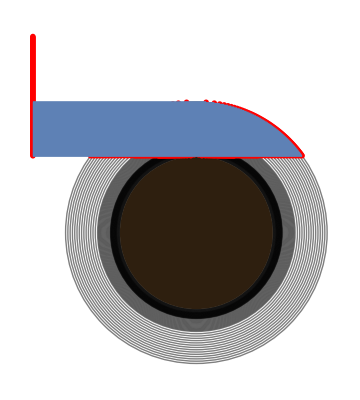

done making ray trace graphic

```mathematica
Print["making ray trace graphic..."];
makeRayTraceGraphic[]
Print["done making ray trace graphic"];
```

```mathematica
Print["interpolating lightcurve..."];
interpolateLC[]
Print["done interpolating lightcurve"];
```

interpolating lightcurve...

done interpolating lightcurve

making lightcurve graphic...

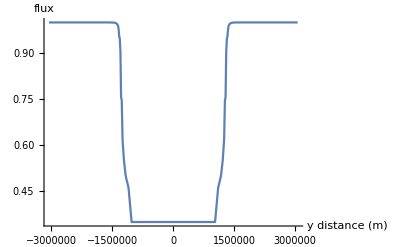

done

```mathematica
Print["making lightcurve graphic..."];
makeLightCurveGraphic[]
Print["done"]
```

## Code for Least Squares Fitting

```mathematica
(*(* called per model *)
modelNumber = 1; (* this number will change with each fit *)
c = 1; (* this is the number of the x-axis point that is moving across the model to sample it *)
makeAtmosphereFromOpticalParams[params,exportFolderPath,modelNumber];
atmosphere = makeAtmosphereFromOpticalParams[Import["C:\\Users\\Hosea\\Dropbox (MIT)\\Academic\\12.ThG\\TestAtmospheres\\constructedAtmosphere"<>IntegerString[modelNumber]<>"1.TSV","HeaderLines"-> 1],1,8,6];
rayTrace[];
interpolateLC[];

(* called per coordinate point *)
twoLimbLC[c];
*)
```